Homework 6
Homework Assignment 6: Protocol design

## Function

```mathematica
PlotPlate[PlateName_,sample_]:=Module[
{width=127.8, length=85.5, xA1=14.4, yA1=11.2, d=9, well, x, y, error},
Labeled[Graphics[
{{EdgeForm[AbsoluteThickness[2]],White,Rectangle[{0,0},{width-d/2,-length+d/2}]},
Table[Text[Style[x+1,16,Bold],{xA1+x*d,-yA1/3}],{x,0,11}],
Table[Text[Style[FromCharacterCode[65+y],20,Bold],{xA1/2.5,-yA1-y*d}],{y,0,7}],
Table[{EdgeForm[AbsoluteThickness[2]],White,Disk[{xA1+x*d,-yA1-y*d},d/2-0.4]},{x,0,11},{y,0,7}],
Table[If[sample[[i]]≠"",
well=ToCharacterCode[sample[[i]]];
error=0;
If[well[[1]]<65 || well[[1]]>72, error=1, y=well[[1]]-65];
Which[
	Length[well]<2 || Length[well]>3, error=1,
	Length[well]==2, If[well[[2]]<49 || well[[2]]>57, error=1, x=well[[2]]-49],
	Length[well]==3, If[well[[2]]!=49 || well[[3]]<48 || well[[3]]>50, error=1, x=10+well[[3]]-49]
];
If[error==1,
Print[sample[[i]]<>" is an incorrect well position"],
{EdgeForm[AbsoluteThickness[2]],Gray,Disk[{xA1+x*d,-yA1-y*d},d/2-0.4]}]],
{i,1,Length[sample]}]
},ImageSize->440],
TextCell[PlateName],Top,LabelStyle->Directive[FontSize->18,FontFamily->"Calibri"]]
];
```

```mathematica
SampleFromSheet[sheet_]:=Table[sheet[[i,1]],{i,2,Length[sheet]}];
```

```mathematica
ExportToPDF[plates_,filename_]:=Module[
{PlatesPerPage, ListOfPages},
PlatesPerPage=Partition[plates,UpTo[4]];
ListOfPages=Table[
Rotate[Grid[Partition[PlatesPerPage[[i]],UpTo[2]],Spacings->{0,2}],90 Degree],
{i,1,Length[PlatesPerPage]}];
Export[filename<>".pdf",CreateDocument[Riffle[ListOfPages,Cell["","PageBreak",PageBreakBelow->True]],Visible->False]]
];
```

```mathematica
FindStrandsInSheet[protocol_,sheet_]:=Module[
{StrandList,start,end,RegularStaple={},PatternStaple={},well,name,sample={}},

StrandList=StringSplit[protocol,"\n"];
start=Position[StrandList,"Internal_Tile_11"][[1,1]]+1;
end=Position[StrandList,"Create Tiles"][[1,1]]-2;
For[i=start,i≤end,i++,
If[StringMatchQ[StrandList[[i]],"   Reg"~~__],
AppendTo[RegularStaple,StringTake[StrandList[[i]],{4,14}]],
AppendTo[PatternStaple,StringTake[StrandList[[i]],{4,19}]]
]];

For[i=2,i<=Length[sheet],i++,
name=sheet[[i,2]];
well[name]=sheet[[i,1]]];
For[i=1,i<=Length[RegularStaple],i++,
If[StringQ[well[RegularStaple[[i]]]],AppendTo[sample,well[RegularStaple[[i]]]]]];
For[i=1,i<=Length[PatternStaple],i++,
If[StringQ[well[PatternStaple[[i]]]],AppendTo[sample,well[PatternStaple[[i]]]]]];
sample];
```

## Plot plate diagrams

Use PlotPlate to generate a plate diagram for your sample:
plate=PlotPlate[sample, plate name]
sample is a list of well positions, for example {“A1”,”B2”,”C3”}.

### A simple example

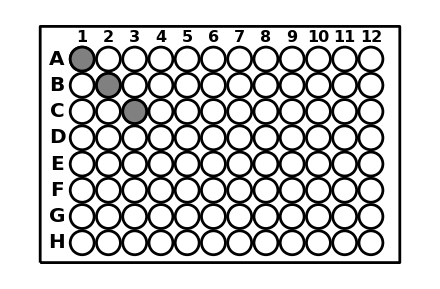
-Graphics-plate name

```mathematica
plate=PlotPlate["plate name",{"A1","B2","C3"}]
```

### A practice plate

```mathematica
sample=Flatten[{
Table["A"<>ToString[x],{x,{4,9}}],
Table["B"<>ToString[x],{x,{3,4,9,10}}],
Table["C"<>ToString[x],{x,2,11}],
Table["D"<>ToString[x],{x,1,12}],
Table["E"<>ToString[x],{x,1,12}],
Table["F"<>ToString[x],{x,2,11}],
Table["G"<>ToString[x],{x,{3,4,9,10}}],
Table["H"<>ToString[x],{x,{4,9}}]
},1];
```

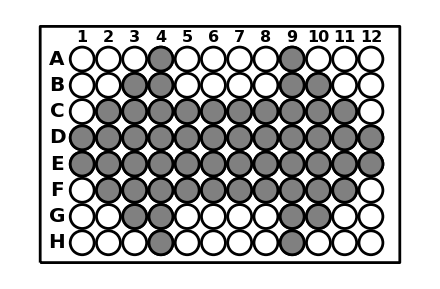
-Graphics-Practice plate: arrow

```mathematica
plate=PlotPlate["Practice plate: arrow",sample]
```

### Stock plates

Use SampleFromSheet to extract the well positions from a spreadsheet:
sample=SampleFromSheet[sheet]
sheet is imported from an excel file.

```mathematica
SetDirectory[NotebookDirectory[]];
SampleSheet=Import["origami_square.xlsx"];
SheetName=Import["origami_square.xlsx","Sheets"];
```

```mathematica
samplelist=Table[{SheetName[[i]],SampleFromSheet[SampleSheet[[i]]]},{i,Length[SampleSheet]}];
```

```mathematica
plates=Table[PlotPlate[samplelist[[i,1]],samplelist[[i,2]]],{i,Length[samplelist]}];
```

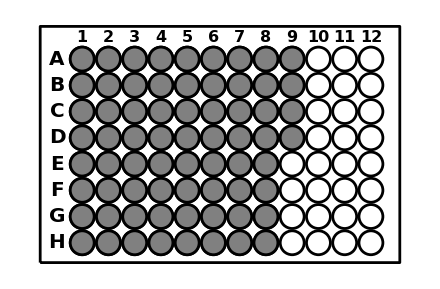
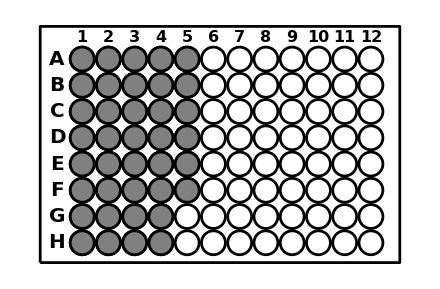
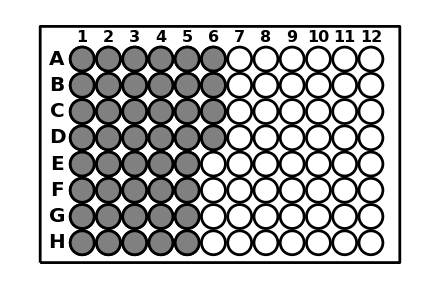
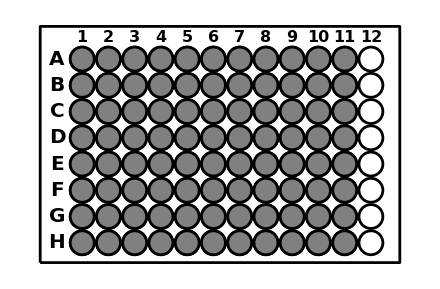
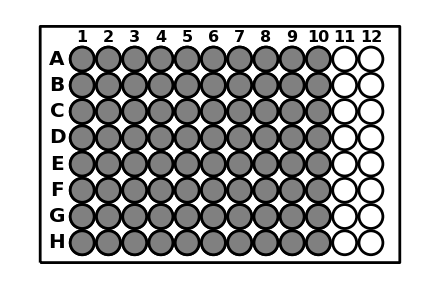
-Graphics-plate1 interior (triangle1&2) | -Graphics-plate2 interior (triangle3&4)
-Graphics-plate3 bridge | -Graphics-plate4 edge (inert)
-Graphics-plate5 pattern (triangle1&2) | -Graphics-plate6 pattern (triangle3&4)
-Graphics-plate7 edge (1nt in 5x5) | -Graphics-plate 8 edge (2nt in 5x5)

```mathematica
Grid[Partition[plates,UpTo[2]]]
```

Modify the code below to select the stock plates that you will use in this lab.

```mathematica
platelist={1,2,3,4};
plates=Table[PlotPlate[samplelist[[i,1]],samplelist[[i,2]]],{i,platelist}];
```

Number of staples in each of the stock plates that you selected:

```mathematica
stapleNumberList=Table[Length[samplelist[[i,2]]],{i,platelist}]
```

{68,68,38,44}

Use ExportToPDF to save the plate diagrams as a PDF file that shows up to four plates per page.

```mathematica
filename="origami_plates_Lab11";
ExportToPDF[plates,filename];
```

```mathematica
mix1vol=stapleNumberList[[1]]+stapleNumberList[[2]]
mix2vol=stapleNumberList[[3]]
mix3vol=stapleNumberList[[4]]
```

136

38

44

```mathematica
intitialStapleConc=10;
mix1stapleConc=intitialStapleConc/mix1vol+0.0
mix2stapleConc=intitialStapleConc/mix2vol+0.0
mix3stapleConc=intitialStapleConc/mix3vol+0.0
```

0.0735294

0.263158

0.227273

Staple Mix 1: 136  µL (68+68 interior staples), 0.0735 µM
Staple Mix 2: 38  µL (38 bridge staples), 0.263 µM
Staple Mix 3: 44  µL (44 edge staples), 0.227 µM

```mathematica
RoundToPipet[vol_]:=Which[
vol≤2,Round[vol/2,0.001]*2,
vol≤20,Round[vol/2,0.01]*2,
vol≤200,Round[vol/2,0.1]*2,
vol≤5000,Round[vol,1]]
```

```mathematica
Options[Mix]={NoInput->False,DisplayProtocol->True};
SetAttributes[Mix,HoldFirst]; (* this allows the volume to be changed if the input strand is to be removed *)
Mix[vol_,specieslist_,samplename_:"Total",OptionsPattern[]]:=Module[
{vollist,volDS,volNoInput},
vollist=Table[specieslist[[i,3]]*vol/specieslist[[i,2]],{i,Length[specieslist]}]; (* pipetting volume of each species *)
volDS=Sum[If[specieslist[[i,4]]=="ds",vollist[[i]],0],{i,Length[vollist]}];
(* total volume of all double-stranded species *)
AppendTo[vollist,(vol-volDS)/10]; (* pipetting volume of 1×TE/10×Mg^(2+) *)
AppendTo[vollist,vol-Total[vollist]]; (* pipetting volume of 1×TE *)
vollist=Table[RoundToPipet[vollist[[i]]],{i,Length[vollist]}];
(* round all volumes to pipet volumes *)
If[OptionValue[NoInput],vol=vol-vollist[[-3]]];
(* if the input strand is to be removed from the mix, subtract its volume from the total volume *)
If[OptionValue[DisplayProtocol],
Grid[Join[
{{"Name","Concentration(uM)", "Volume(uL)"},
{"1×TE","",vollist[[-1]]},
{"1×TE/10×Mg^(2+)","",vollist[[-2]]}},
Table[{specieslist[[i,1]],specieslist[[i,2]],vollist[[i]]},{i,Length[specieslist]-If[OptionValue[NoInput],1,0]}],
{Style[#,Bold]&/@{samplename,"",vol}}],
Alignment->Right,Frame->All,
Background->{None,{-1->LightGray}}]]]
```

```mathematica
Mix[50,{{"M13",0.370,10*10^-3,"ss"},{"Interior Staple Mix",mix1stapleConc,30*10^-3,"ss"},{"Bridge Staple Mix",mix2stapleConc,30*10^-3,"ss"},{"Edge Staple Mix",mix3stapleConc,30*10^-3,"ss"}}]
```

Name | Concentration(uM) | Volume(uL)
1×TE |  | 10.94
1×TE/10×Mg^(2+) |  | 5.
M13 | 0.37 | 1.352
Interior Staple Mix | 0.0735294 | 20.4
Bridge Staple Mix | 0.263158 | 5.7
Edge Staple Mix | 0.227273 | 6.6
Total |  | 50